## Integrate-and-Fire neural network that admits postsynaptic currents

```mathematica
$PlotTheme="Scientific";
```

```mathematica
timeconstant=R=4; 
threshold=10;
T=10;
```

Function for generation of Erdös-Renyi model

```mathematica
weightedNet[n_,p_]:= Module[{ g, Wnet},
 g = RandomGraph[BernoulliGraphDistribution[n,p],DirectedEdges->True,VertexLabels->"Name"];
 Wnet = Graph[g,EdgeWeight->RandomReal[{-1,1},EdgeCount[g]]];
 Return[Wnet]
 ]
```

Postsynaptic current. It cannot be negative, that is why we use the Ramp function in PSC2.

```mathematica
PSC[spikingtime_,t_]:=(-(t-spikingtime)^(2/3)+6)HeavisideTheta[t-spikingtime]
```

```mathematica
PSC2[spikingtime_,t_]:=Ramp[PSC[spikingtime,t]]
```

The postsynaptic current is of the following form

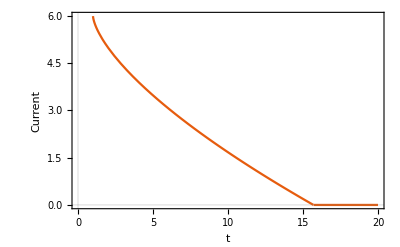

```mathematica
Plot[PSC2[1,t],{t,0,20},FrameLabel->{t,"Current"}]
```

Initial homogeneous perturbation for neural network

```mathematica
inInit[externalInput_,n_] := Table[externalInput,n]
```

Calculate firing rate from time t0 to t1. Returns a list of firing rates of all neurons. Default value for the initial time is 0.

```mathematica
firingRate[tableST_,t0_:0,t1_]:=Module[{FR},
FR=Table[Length[Select[tableST⟦i⟧,t0<#<t1&]]/(t1-t0),{i,1,Length[tableST]}];
Return[FR]
]
```

Calculates global firing rate from time t0 to t1. Default value for the initial time is again 0.

```mathematica
PoblationalFR[tableST_,t0_:0,t1_]:=Mean[firingRate[tableST,t0,t1]]
```

Function that updates the inputs of each neuron after a spiking time.

```mathematica
inGen[graph_,node_,spikingtime_,in_]:=
		Module[{WM, input = in, k, adj={}},
		WM=Normal[WeightedAdjacencyMatrix[graph]];
		For[k=1, k≤Length[node],k++,
			Table[
				If[ MemberQ[ Select[VertexOutComponent[graph,node⟦k⟧,1],#≠node⟦k⟧&], i],
					input⟦i⟧+=WM⟦node⟦k⟧,i⟧*PSC2[spikingtime,t]
					],
			{i,1,Length[in]}];
		];
		Return[input]
	];
```

```mathematica
varsGen[n_]:= Table[ToExpression["u[t]"],{i,n}];
```

Function that gives the initial conditions of the system of differential equations. It changes each spiking time.

```mathematica
ciGen[index_,sols_,st_,ic_,n_]:= 
		Module[{ci = ic},
				ci=Table[
					If[ MemberQ[index,i],
						ci⟦i⟧=0,
						ci⟦i⟧=u[t]/.sols⟦i⟧/.t-> st],
				{i,1,n}];
		Return[ci]]
```

System of differential equations following the Integrate-and-Fire model

```mathematica
sisGen[vars_,input_]:=Table[timeconstant D[vars⟦i⟧,t]==(-vars⟦i⟧+ R input⟦i⟧)HeavisideTheta[vars⟦i⟧+15],{i,1,Length[vars]}];
```

Simulate dynamics of neural network on graph G

```mathematica
netSim[G_, treshold_,externalinput_List,Δw_]:=
	Module[{n, Gw, weightMatrix,sis, sols, newST=0, ic, Δt=10^-5, U, i0,
			TableInputs, TableST, TableVoltageFunctions={}, 
			listST={1}, orderedST={}, indexST={}, index, voltageFunctions},
		n=VertexCount[G];
		weightMatrix=WeightedAdjacencyMatrix[G]/.x_/;x==0->Infinity;
		(*Perturbing the weights if Δw ≠ 0*)
		If[Δw==0, ,{
		Table[If[weightMatrix⟦i,j⟧==Infinity,,weightMatrix⟦i,j⟧=Max[Min[1,weightMatrix⟦i,j⟧+Δw],-1]],{i,1,n},{j,1,n}];
		}];
		(*Generating new network with weights perturbed*)
		Gw = WeightedAdjacencyGraph[weightMatrix];
		ic= Table[0,n];
		TableST=Table[{},n];
		(*TableInputs[t_] = inInit[externalinput,n];*)
		TableInputs[t_]=externalinput;
		U[t_] = varsGen[n];
		While[ listST ≠ {},
				listST = {};
				sis = sisGen[ U[t], TableInputs[t] ];
				sols = Flatten@Table[ NDSolve[Flatten@{
						sis⟦i⟧, u[ newST+Δt ] == ic⟦i⟧,
							WhenEvent[{u[t]==treshold},{AppendTo[listST,{i,t}],"StopIntegration"}]},
							U[t]⟦ i ⟧,{t,newST+Δt,T}],
						{i,1,Length[U[t]]}
						];	
				index = listST⟦ Flatten[ Position[ listST⟦;;,2⟧, Min[listST⟦;;,2⟧] ],1],1 ⟧;
				newST = Min[listST⟦;;,2⟧];
				TableInputs[t_] = inGen[Gw,index,newST,TableInputs[t]];
				ic = ciGen[index,sols,newST,ic,n];
				AppendTo[indexST,index];
				AppendTo[orderedST,newST];
				AppendTo[TableVoltageFunctions,sols];
				Table[If[MemberQ[index,i],AppendTo[TableST⟦i⟧,newST]],{i,1,n}];
		];
		voltageFunctions = Table[
				Piecewise[Table[
						{TableVoltageFunctions⟦j,i⟧, If[j==1,0<t≤orderedST⟦j⟧,orderedST⟦j-1⟧ < t ≤ orderedST⟦j⟧]},
					{j,1,Length[orderedST]}]],
				{i,1,Length[TableVoltageFunctions⟦1,;;⟧]}
		];
	Return[{indexST, voltageFunctions, TableST}]
	]
```

Simulate dynamics of neural network on Erdös-Renyi graph of n nodes and p probability.

```mathematica
netSim[n_, p_, treshold_,externalinput_List,Δw_]:=
	Module[{net, indexST={},voltageFunctions, TableST},
		net = weightedNet[n,p];
		{indexST, voltageFunctions, TableST}= netSim[net,treshold,externalinput,Δw];
	Return[{net,indexST, voltageFunctions, TableST}]
	]
```

Shows the plot of the spiking times

```mathematica
(*SPIKING TRAIN*)
spktrnF[data_,opts:OptionsPattern[]]:=Module[{
options={ChartBaseStyle->EdgeForm[None],ChartElementFunction->"LineDensity",BarOrigin->Left,BarSpacing->0.1,ChartLabels->Range[Length@data]}},
DistributionChart[data,If[opts==={},options,PrependTo[options,{opts}]]]]
```